```mathematica
(*Quit[]*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
(* Zhi-hui Wang, Guo-Li Wang, Chao-Hsi Chang,  arXiv:1107.0474 [hep-ph],     J.Phys.G 39 (2012) 015009 *)
```

## Init

```mathematica
<<MyPackages`ChDim`
```

```mathematica
<<MyPackages`HistV2`
```

```mathematica
SetOptions[ChDim, Dimensions->{
GF->-2,
a1->0, beta->0, Vbc->0, Vuq->0,
mu->0,a->0, b->0,
rhoL[_]->0, rhoT[_]->0,
fPlus[_]->0, fMinus[_]->0,
hA[_]->0, hV1[_]->0, hV2[_]->0, hV3[_]->0,
tV[_]->0, tA1[_]->0, tA2[_]->0, tA3[_]->0,
fP->1, mP->1, fV->1, mV->1,
p1->1, p2->1,q->1, MBc->1, Mcc->1,
q2->2}];
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
<<"./mdat/wang_ff.mdat";
```

## Intro

```mathematica
GeV=1.; MeV=10^-3 GeV;
```

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
getMcc[out_]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
```

```mathematica
$MBc = 6274.47MeV;
$mPi = 0.140GeV;
$a1 = 1.14;
Clear[Ngamma];
Ngamma[out_, outL_]:=Module[{
$Mcc=getMcc[out],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2],
fffit = ffFitRule$Wang
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->$a1
}//.{MBc -> $MBc, mPi->$mPi, mV->775MeV, Mcc->$Mcc, q2->$q2}/.fffit]
Ngamma[out_, "enu"]:=Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}
```

```mathematica
Clear[q2Max];
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
Clear[extractNames];
extractNames[json_]:=Module[{names = json⟦3,2,All,1,2⟧}, Table[{i,names⟦i⟧},{i,Length[names]}]];
```

```mathematica
Clear[getFileNameName];
Options[getFileName]={Var->"m2_0m1"};
getFileName[out_, mode_, ff_, OptionsPattern[]]:="../c++/results/B_c+_"<>out<>"_"<>mode<>"_ff"<>ff<>"/"<>OptionValue[Var]<>".txt";
getFileName[out_, mode_, opt:OptionsPattern[]]:=getFileName[out, mode, "1", opt];
```

```mathematica
Clear[readROOT];
Options[readROOT]={Norm->False, Color->Red};
readROOT[fileName_,OptionsPattern[]]:=Module[{root},
root = ReadList[fileName,{Number,Number,Number}];
root = HST2D[{#⟦1⟧,#⟦2⟧±#⟦3⟧}&/@root, PlotStyle->OptionValue[Color]];
If[!OptionValue[Norm]=!=False,
root *= OptionValue[Norm]/IntegralHST[root];
];
root
]
```

## Wang, e-spectrum

```mathematica
json = Import["../literatute/1107.0474/Fig5_e.json"];
extractNames[json]
```

{{1,chi_c0},{2,chi_c1},{3,chi_c2}}

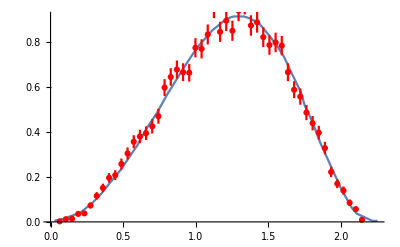

```mathematica
pap =HST2D[ extractFF[json, 1]["data"]];
pap /= IntegralHST[pap];
root = readROOT[getFileName["chi_c0","enu","2",Var->"e_2"], Norm->1];
Show[
PlotHST[pap, Joined->True], PlotHST[root]
]
```

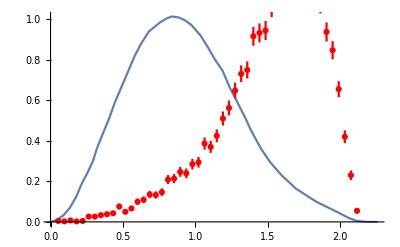

```mathematica
pap =HST2D[ extractFF[json, 2]["data"]];
pap /= IntegralHST[pap];
root = readROOT[getFileName["chi_c1","enu","2",Var->"e_2"], Norm->1];
Show[
PlotHST[pap, Joined->True], PlotHST[root]
]
```

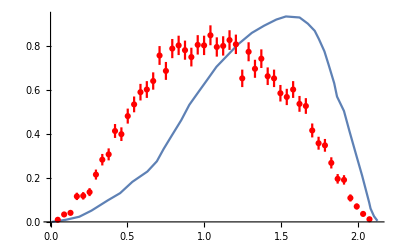

```mathematica
pap =HST2D[ extractFF[json, 3]["data"]];
pap /= IntegralHST[pap];
root = readROOT[getFileName["chi_c2","enu","2",Var->"e_2"], Norm->1];
Show[
PlotHST[pap, Joined->True], PlotHST[root]
]
```